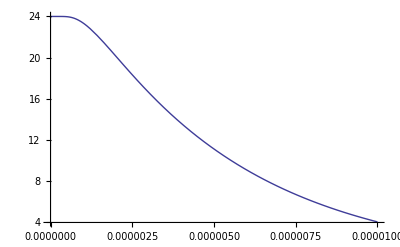

```mathematica
a = 4;
b = 100;
al = (0.9*2.66*^6/117)^-1;
perc[l_,t_]:=Sum[2*(1-(-1)^n)*(b/a-1)*Sin[n*π/2]*Exp[-n^2*π^2*t/(al*l^2)]/(π*n),{n,1,100}];
Plot[perc[1,t],{t,0,.00001}]
```